1. NALOGA

```mathematica
Simplify[(x^5-2x^2+3x+4)/(x^5-2x-1)]/.x->{1,2,3,4}
```

{-3,34/27,119/118,144/145}

```mathematica
Table[(x^5-2x^2+3x+4)/(x^5-2x-1),{x, 1, 10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

2. NALOGA

```mathematica
sez = {10, 20, 30, 40, 50, 60, 70}
```

{10,20,30,40,50,60,70}

```mathematica
sez3=Take[sez, 3]
```

Take::normal: Nonatomic expression expected at position 1 in Take[sez,3].

```mathematica
Take[sez,3]
```

{10,20,30}

```mathematica
sez3
```

{10,20,30}

```mathematica
sezminus2=Take[sez, -2]
```

{60,70}

```mathematica
sezoddrugidocetrti=Take[sez,{2,4}]
```

{20,30,40}

```mathematica
sez235=sez[[ {2, 3, 5}]]
```

{20,30,50}

```mathematica
sezraz4i5=Drop[sez, {4,5}]
```

{10,20,30,60,70}

3. NALOGA

```mathematica
ClearAll[sez]
```

```mathematica
sez={x^6, x^2,a}
ReplaceAll[sez,x->3]
```

{x^6,x^2,a}

```mathematica
sez/.x->3
```

{729,9,a}

```mathematica
ReplaceAll[sez, x^2->x]
```

{x^6,x,a}

```mathematica
ReplaceAll[sez,x->{1,2,3}]
```

{{1,64,729},{1,4,9},a}

```mathematica
ReplaceAll[sez,{x->3,a->x}]
```

{729,9,x}

```mathematica
če bi bila pogoj za x in pogoj za a v posebaj zavitih oklepajih ti nato vrne dva seznama prvo za prvi pogoj in nato se drugi za drugi pogoj
```

```mathematica
sez//.{x->3,a->x}
```

{729,9,3}

```mathematica
seznov= NE znam!
```

4. NALOGA

```mathematica
f[x_]:=x^5+4x^3-9
D[f[x],x]
```

12 x^2+5 x^4

```mathematica
D[f[x],x]/.x->{1,5}
```

{17,3425}

```mathematica
f[x_]:=E^(x^(1/4))
D[f[x],x]
```

(ⅇ^(x^(1/4)))/(4 x^(3/4))

```mathematica
D[f[x],x]/.x->{1,2}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

```mathematica
FullSimplify[D[Abs[x+1],x],x ∈Reals]
```

Sign[1+x]

```mathematica
tam ko je ena plus x pozitivn tam ko je ena minus x je negativen
```

Sign[1+x]

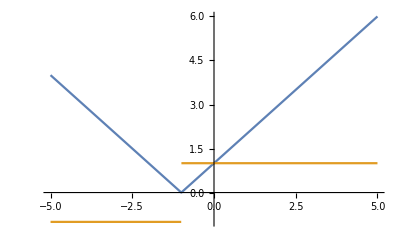

```mathematica
resitev=FullSimplify[D[Abs[x+1],x],x ∈Reals]
Plot[{Abs[x+1],resitev}, {x,-5,5}]
```

```mathematica
f[x_]:=a x^2+3b
D[f[x],x]
```

2 a x

```mathematica
D[f[x],x]/.x->{1,2}
```

{2 a,4 a}

5. NALOGA

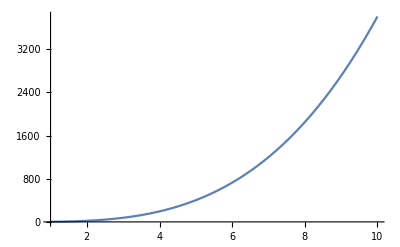

```mathematica
f[x_]:=x^3Log[4x+5]
Plot[f[x],{x,1,10}]
```

```mathematica
vrednost=f[5]
```

125 Log[25]

```mathematica
x0=5
```

5

```mathematica
k0=D[f[x],x]/.x->x0
```

20+75 Log[25]

```mathematica
n0=n/.First[Solve[f[x0]==k0*x0+n,n]]
```

-50 (2+5 Log[25])

```mathematica
t[x_]:=k0*x+n0
```

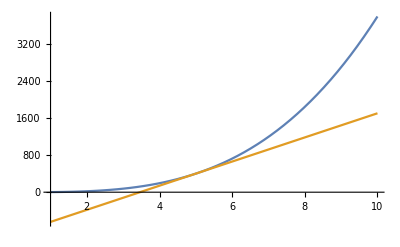

```mathematica
Plot[{f[x], t[x]},{x,1,10}]
```

```mathematica
narisi[x0_]:=Module[{k0,n0,t},
k0=D[f[x],x]/.x->x0;
n0=n/.First[Solve[f[x0]==k0*x0+n,n]];
t[x_]:=k0*x+n0;
Plot[{f[x], t[x]},{x,1,10}]
]
```

```mathematica
Manipulate[narisi[x0],{x0,1,10}]
```

```mathematica
Manipulate[Expand[(x+1)^i],{i,1,10,1}]
```

```mathematica
narisi[x0_,f_]:=Module[{k0,n0,t},
k0=D[f[x],x]/.x->x0;
n0=n/.First[Solve[f[x0]==k0*x0+n,n]];
t[x_]:=k0*x+n0;
Plot[{f[x], t[x]},{x,1,10}]
]
```

```mathematica
Manipulate[narisi[x0,Sin],{x0,1,10}]
```